## Manual for spNDSolve.m (To be completed)

The Mathematica package spNDSolve.m (by Jie Ren, available at (https://github.com/renphysics/spNDSolve) is designed for solving PDEs by the pseudospectral method.

### Install and load the package

Put the file spNDSolve.m in the following directory (or the same directory as the working notebook)

```mathematica
SystemOpen@FileNameJoin[{$UserBaseDirectory,"Applications"}]  (*Put "*.m" in*)
```

Load the package by running

```mathematica
<<spNDSolve.m
```

### Example 1: Holographic superconductors in 0803.3295 (HHH)

We start from the two coupled equations. They are copied from Herzog’s notebook by the shooting method.

```mathematica
restart[];
flist={psi[z],phi[z]};
eqlist={(-z+z^4+phi[z]^2) psi[z]+(-1+z^3) (3 z^2 psi'[z]+(-1+z^3) psi''[z]),2 phi[z] psi[z]^2+(-1+z^3) phi''[z]}; (*Equations of motion*)
bdylist1={psi'[z],phi[z]-mu}; (*Boundary conditions at z=0*)
bdylist2={3 z^2 psi'[z]-2psi[z],phi[z]}; (*Boundary conditions at z=1*)
eqProcess[flist,eqlist,{{z==0,bdylist1},{z==1,bdylist2}}]; (*Impose boundary conditions*)
calcfref:=(psi=one; phi=mu one;);  (*Initial guess of the solution*)
output:=(solsave);
```

```mathematica
spNDSolve[z,linearMap[{0,1}],60,{mu,2}];
```

```mathematica
phi
```

{2.,1.99863,1.99452,1.98769,1.97815,1.96593,1.95106,1.93358,1.91355,1.89101,1.86603,1.83867,1.80902,1.77715,1.74314,1.70711,1.66913,1.62932,1.58779,1.54464,1.5,1.45399,1.40674,1.35837,1.30902,1.25882,1.20791,1.15643,1.10453,1.05234,1.,0.947664,0.895472,0.843566,0.792088,0.741181,0.690983,0.641632,0.593263,0.54601,0.5,0.455361,0.412215,0.37068,0.330869,0.292893,0.256855,0.222854,0.190983,0.161329,0.133975,0.108993,0.0864545,0.0664196,0.0489435,0.0340742,0.0218524,0.0123117,0.0054781,0.00137047,0.}

### Example 1’: Holographic superconductors in 0803.3295 (HHH)

This example is the same as the last one, but with difference in details. (1) the equations of motion contain a function f[z] (2) there singularities at z=1. (3) save equations to a file

```mathematica
setdir;
flist={psi[z],phi[z]};
reflist={f[z]}; (*other functions in equations*)
eqlist={(z ((-z+z^4+phi[z]^2) psi[z]+(-1+z^3) (3 z^2 psi'[z]+(-1+z^3) psi''[z])))/((-1+z^3)^2),(2 phi[z] psi[z]^2+(-1+z^3) phi''[z])/(-1+z^3)};
eqProcess[{flist},put[eqlist]];
```

Once the equations of motion are saved to a file “eqlistmat”, the follwing is the code to run.

```mathematica
restart[];
flist={psi[z],phi[z]}; (*unkown functions to be solved*)
reflist={f[z]}; (*other functions in equations*)
bdylist1={3 z^2 psi'[z]-2psi[z],phi[z]}; (*Boundary conditions at z=0*)
bdylist2={psi'[z],phi[z]-mu}; (*Boundary conditions at z=1*)
eqProcess[{flist,reflist},get[eqlistmat,z->zaux12],{{z==0,bdylist1},{z==1,bdylist2}}];  (*load equations from a file; replace z with zaux12 to avoid singularities at two boundaries*)(*Jacobian of boundary conditions*)
calcfref:=(psi=one; phi=mu one; f=1-z^3);  (*Initial guess of the solution*)
calcref:=(f=1-z^3);
output:=(solsave);
```

```mathematica
Dynamic[changes]
```

```mathematica
spNDSolve[z,linearMap[{0,1}],nz,{nz,{50,60}},{mu,2},eqlistmatQ->True];
```

```mathematica
outputs
```

{{{9.90424×10^-27,0.001398,0.00529115,0.0119612,0.0210812,0.0329212,0.0471215,0.0639494,0.083006,0.104566,0.128188,0.154166,0.18201,0.212052,0.243754,0.277497,0.312694,0.349798,0.388166,0.428338,0.469617,0.512642,0.556653,0.6024,0.649053,0.697482,0.746767,0.797906,0.849863,0.903772,0.958437,1.01512,1.07241,1.13168,1.19115,1.25228,1.31267,1.37373,1.43195,1.48829,1.53701,1.57762,1.5994,1.59748,1.54866,1.43467,1.1961,0.773513,-0.00954228,-1.10105,-1.28227},{3.95669×10^-27,0.00126123,0.00503884,0.011319,0.0200759,0.031276,0.044874,0.0608175,0.0790423,0.0994781,0.122043,0.146651,0.173204,0.201603,0.231737,0.263499,0.296771,0.33144,0.367392,0.404518,0.442712,0.481879,0.521934,0.562806,0.604439,0.646799,0.689869,0.733663,0.778209,0.823576,0.869849,0.917157,0.965644,1.0155,1.06693,1.12017,1.17547,1.23311,1.29333,1.35636,1.42234,1.49129,1.56297,1.63681,1.71156,1.78522,1.85441,1.91457,1.95999,1.98834,2.},{((#1--1) (1-0))/(1--1)+0&,50}},{{-4.48104×10^-26,0.00115643,0.00435434,0.00985431,0.0173696,0.0271548,0.0389035,0.052869,0.0687211,0.0867179,0.106501,0.128341,0.151848,0.17731,0.204304,0.233147,0.263381,0.295357,0.32858,0.36345,0.399432,0.436982,0.475525,0.515582,0.556535,0.59898,0.642251,0.687028,0.732591,0.779712,0.82761,0.877156,0.9275,0.979619,1.03258,1.08747,1.14326,1.20116,1.25999,1.32112,1.38316,1.44762,1.51284,1.58044,1.64834,1.71823,1.78725,1.85704,1.92333,1.9872,2.04153,2.08557,2.10582,2.09587,2.02606,1.87258,1.5585,1.00606,-0.0149353,-1.43808,-1.67436},{-2.91231×10^-28,0.00070333,0.00281048,0.00631659,0.0112111,0.0174816,0.0251099,0.034076,0.0443545,0.0559182,0.0687345,0.0827694,0.0979837,0.114337,0.131786,0.150283,0.169781,0.19023,0.211579,0.233778,0.256775,0.280523,0.304972,0.330082,0.355811,0.382126,0.408999,0.436412,0.464352,0.492821,0.521826,0.551394,0.581558,0.612374,0.643905,0.676239,0.709475,0.74374,0.779169,0.815935,0.854214,0.894224,0.936189,0.980372,1.02704,1.0765,1.12904,1.18499,1.24462,1.30821,1.3759,1.44773,1.52341,1.6023,1.68299,1.76321,1.83909,1.90541,1.95557,1.98694,2.},{((#1--1) (1-0))/(1--1)+0&,60}}}

```mathematica
eqLinearize[{flist},{eqlist,"eqlist","mat"}]
```

```mathematica
spNDSolve[z,linearMap[{0,1}],20,{rh,1}]
```

### Example 3: holographic

```mathematica
restart[];
flist={g[z],h[z],phi[z]};
myV[ϕ_]:=(2 ⅇ^(-ϕ/α) (α^2-8 ⅇ^(((1+α^2) ϕ)/(2 α)) α^2-3 α^4+ⅇ^(ϕ/α+α ϕ) (-3+α^2)))/((1+α^2)^2);
myZA[ϕ_]:=1;
eqlist={2 myV[phi[z]]+(z^4 ρ^2)/myZA[phi[z]]-4 z g'[z]+g[z] (12+z^2 phi'[z]^2),2 h'[z]-z h[z] phi'[z]^2,-z^2 g[z] h'[z] phi'[z]+h[z] (-2 myV'[phi[z]]+z ((z^3 ρ^2 myZA'[phi[z]])/myZA[phi[z]]^2-4 g[z] phi'[z]+2 z g'[z] phi'[z]+2 z g[z] phi''[z]))};
bdylist1={g[z],h[z]-1,phi''[z]-2κ phi'[z]};
bdylist2={g[z],h[z]-1,-2 myV'[phi[z]]+(ρ^2 myZA'[phi[z]])/myZA[phi[z]]^2+2 g'[z] phi'[z]};
eqProcess[{flist},eqlist,{{{z==0,{2,3}},bdylist1},{{z==1,{1,3}},bdylist2}}];
calcfref:=(g=1/5(1-z); h=one; phi=(1/2z+1/4 z^2););
output:={(-(dz.g)/(4Pi √h(-κ)))[[-1]],((dz.phi)/-κ)[[1]],(4Pi)/κ^2,1/(-κ)^3(-1/3 dz.dzz.(g/h))[[1]],1/(-κ)^3(1/6 dz.dzz.g-1/4(dz.phi)(dzz.phi))[[1]],3/(4Pi(-κ)),-1/(-κ)^3,κ,1/(-κ)^3(-1/3 dz.dzz.g+3/4(dz.phi)(dzz.phi))[[1]],solsave}; 
(*T/(-κ), O/(-κ), s/κ^2, ϵ0/(-κ)^3, F/(-κ)^3; Ts=3/2 ϵ0*)
outT:=outputs[[;;,1]];
outO:=outputs[[;;,2]];
outS:=outputs[[;;,3]];
outF:=outputs[[;;,5]];
outT0:=outputs[[;;,6]];
outF0:=outputs[[;;,7]];
outκ:=outputs[[;;,8]];
outM:=outputs[[;;,9]];
outphih:=outputs[[;;,-1,3,-1]];
Off[LinearSolve::luc];
Dynamic[changes]
```

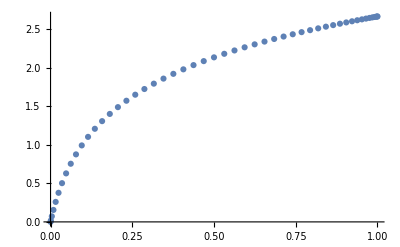

```mathematica
spNDSolveD[z,{linearMap[{0,1}],50},{α,0.3,0.4,0.1},{ρ,0.},{κ,-2,-10,-1/2},minPrec->MachinePrecision];
ListPlot[{z,phi}ᵀ]
```

```mathematica
outM
```

{-0.0183651,-0.310527,-0.449794,-0.512874,-0.545646,-0.564393,-0.575912,-0.58339,-0.588463,-0.59203,-0.594614,-0.596533,-0.597989,-0.599115,-0.600001,-0.600709,-0.601283,-0.601756}

```mathematica
spNDSolveD[z,{linearMap[{0,1}],50},{α,4/10},{ρ,0},{κ,-1/2,-35/100,1/100},epValue->10^-8,minPrec->34]; (*phi>0, increse T*)
```

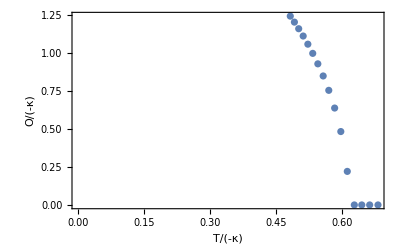

```mathematica
ListPlot[outputs[[;;,{1,2}]],PlotRange->All,frameLabel["T/(-κ)","O/(-κ)"],AxesOrigin->{0,0}]
```

### spNDSolve

```mathematica
Options[spNDSolve]
```

{auxreplQ→False,calcrefredQ→False,epValue→1/1000000000,eqlistmatQ→False,iniQ→True,linearQ→False,lsqrQ→False,maxChange→1000000000,minPrec→0,D→False}

epValue: When the change for an iteration is smaller than the epValue, the iteration will stop

eqlistmatQ: If the equations and there Jacobian are saved to an optimized file, this option must be set to be True.

iniQ: If this is True, then the initial guess of the solution calcfref. If it is False, then not run calcfref.

linearQ: If the equations are linear, this must be set to be True.

lsqrQ: If this is True, then use LeastSquare instead of LinearSolve

minPrec: If it is zero, then use machine precision. If it is nonzero, then use

“D”->n: Delete the rows and columns corresponding to boundaries with label n.

### cheb: Construct the grid

The function for constructing the grid is cheb. It has flexible capabilities by different formats.

```mathematica
cheb[x,8]
```

```mathematica
dx//MatrixForm
```

(-21.5 | 26.2741 | -6.82843 | 3.23983 | -2. | 1.44646 | -1.17157 | 1.03957 | -0.5
-6.56854 | 3.15432 | 4.61313 | -1.84776 | 1.08239 | -0.765367 | 0.613126 | -0.541196 | 0.259892
1.70711 | -4.61313 | 0.707107 | 3.08239 | -1.41421 | 0.917608 | -0.707107 | 0.613126 | -0.292893
-0.809957 | 1.84776 | -3.08239 | 0.224171 | 2.61313 | -1.30656 | 0.917608 | -0.765367 | 0.361616
0.5 | -1.08239 | 1.41421 | -2.61313 | 0. | 2.61313 | -1.41421 | 1.08239 | -0.5
-0.361616 | 0.765367 | -0.917608 | 1.30656 | -2.61313 | -0.224171 | 3.08239 | -1.84776 | 0.809957
0.292893 | -0.613126 | 0.707107 | -0.917608 | 1.41421 | -3.08239 | -0.707107 | 4.61313 | -1.70711
-0.259892 | 0.541196 | -0.613126 | 0.765367 | -1.08239 | 1.84776 | -4.61313 | -3.15432 | 6.56854
0.5 | -1.03957 | 1.17157 | -1.44646 | 2. | -3.23983 | 6.82843 | -26.2741 | 21.5)

```mathematica
dx.x
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
dxx.x^2
```

{2.,2.,2.,2.,2.,2.,2.,2.,2.}

In the above example, cheb[x, 8] can be cheb[u, 8], then the variable will be u, and differential matrix is du and duu.     id is the idensity matrix, zero is the zero matrix, and one is a vector of 1’s.

```mathematica
cheb[x,#&,8]
```

```mathematica
cheb[x,(#+1)/2&,8]
```

```mathematica
cheb[x,linearMap[{0,1}],8]
```

linearMap[{x1, x2} -> {y1, y2}] generates a pure function that linearly maps the interval (x1, x2) to (y1, y2). linearMap[{x1, x2}] generates a pure function that linearly maps the interval (x1, x2) to (-1, 1).

```mathematica
cheb[x,{10,"periodic"}]
```

```mathematica
x
```

{0.,0.571199,1.1424,1.7136,2.28479,2.85599,3.42719,3.99839,4.56959,5.14079,5.71199}

```mathematica
dx.Sin[x]
```

{1.,0.841254,0.415415,-0.142315,-0.654861,-0.959493,-0.959493,-0.654861,-0.142315,0.415415,0.841254}

```mathematica
Cos[x]
```

{1.,0.841254,0.415415,-0.142315,-0.654861,-0.959493,-0.959493,-0.654861,-0.142315,0.415415,0.841254}

```mathematica
cheb[x,{10,4}]
```

```mathematica
x
```

{-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.}

```mathematica
dx//MatrixForm
```

(-10.4167 | 20. | -15. | 6.66667 | -1.25 | 0 | 0 | 0 | 0 | 0 | 0
-1.25 | -4.16667 | 7.5 | -2.5 | 0.416667 | 0 | 0 | 0 | 0 | 0 | 0
0.416667 | -3.33333 | 0 | 3.33333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.416667 | -3.33333 | 0 | 3.33333 | -0.416667 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.416667 | -3.33333 | 0 | 3.33333 | -0.416667 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.416667 | -3.33333 | 0 | 3.33333 | -0.416667 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.416667 | -3.33333 | 0 | 3.33333 | -0.416667 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.416667 | -3.33333 | 0 | 3.33333 | -0.416667 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.416667 | -3.33333 | 0 | 3.33333 | -0.416667
0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 2.5 | -7.5 | 4.16667 | 1.25
0 | 0 | 0 | 0 | 0 | 0 | 1.25 | -6.66667 | 15. | -20. | 10.4167)

cheb[x, {10, 4, "cheb"}] or cheb[x, {10, 4, “periodic”}]

```mathematica
cheb[x1,linearMap[{0,0.2}],6,"1"]
cheb[x2,linearMap[{0.2,1}],8,"2"]
```

```mathematica
cheb[{x,y},{10,10}]
```

```mathematica
cheb[{x,y},{#&,#&},{10,10}]
```

```mathematica
cheb[{z,x},{linearMap[{0,1}],#&},{20,{20,"periodic"}}]
```

```mathematica
cheb[{z1,x1},{linearMap[{0,0.2}],#&},{20,{20,"periodic"}},"1"]
cheb[{z2,x2},{linearMap[{0.2,1}],#&},{20,{20,"periodic"}},"2"]
```

```mathematica
cheb[x,8]
```

```mathematica
x                                                      (*Collocation points*)
```

{-1.,-0.92388,-0.707107,-0.382683,0.,0.382683,0.707107,0.92388,1.}

```mathematica
f=1-x^3                                      (*A function is a vector*)
```

{2.,1.78858,1.35355,1.05604,1.,0.943957,0.646447,0.211419,0.}

```mathematica
dx//MatrixForm                      (*Differentiation matrix*)
```

(-21.5 | 26.2741 | -6.82843 | 3.23983 | -2. | 1.44646 | -1.17157 | 1.03957 | -0.5
-6.56854 | 3.15432 | 4.61313 | -1.84776 | 1.08239 | -0.765367 | 0.613126 | -0.541196 | 0.259892
1.70711 | -4.61313 | 0.707107 | 3.08239 | -1.41421 | 0.917608 | -0.707107 | 0.613126 | -0.292893
-0.809957 | 1.84776 | -3.08239 | 0.224171 | 2.61313 | -1.30656 | 0.917608 | -0.765367 | 0.361616
0.5 | -1.08239 | 1.41421 | -2.61313 | 0. | 2.61313 | -1.41421 | 1.08239 | -0.5
-0.361616 | 0.765367 | -0.917608 | 1.30656 | -2.61313 | -0.224171 | 3.08239 | -1.84776 | 0.809957
0.292893 | -0.613126 | 0.707107 | -0.917608 | 1.41421 | -3.08239 | -0.707107 | 4.61313 | -1.70711
-0.259892 | 0.541196 | -0.613126 | 0.765367 | -1.08239 | 1.84776 | -4.61313 | -3.15432 | 6.56854
0.5 | -1.03957 | 1.17157 | -1.44646 | 2. | -3.23983 | 6.82843 | -26.2741 | 21.5)

```mathematica
dx.f
```

```mathematica
cheb[x,(#+1)/2&,20]
```

```mathematica
cheb[x,linearMap[{0,1}],8]
```

```mathematica
cheb[x,{20,"periodic"}]
```

```mathematica
cheb[x,linearMap[{0,1}],{50,4}]
```

```mathematica
cheb[{z,x},{linearMap[{0,1}],#&},{20,{20,"periodic"}}]
```

```mathematica
cheb[{z1,x1},{linearMap[{0,0.2}],#&},{20,{20,"periodic"}},"1"]
cheb[{z2,x2},{linearMap[{0.2,1}],#&},{20,{20,"periodic"}},"2"]
```